```mathematica
Stair[angle_]= Cot[angle]
```

Cot[angle]

```mathematica
Distance[angle_]=Cot[angle]/Abs[Cot[angle]-Round[Cot[angle]]]
```

Cot[angle]/Abs[Cot[angle]-Round[Cot[angle]]]

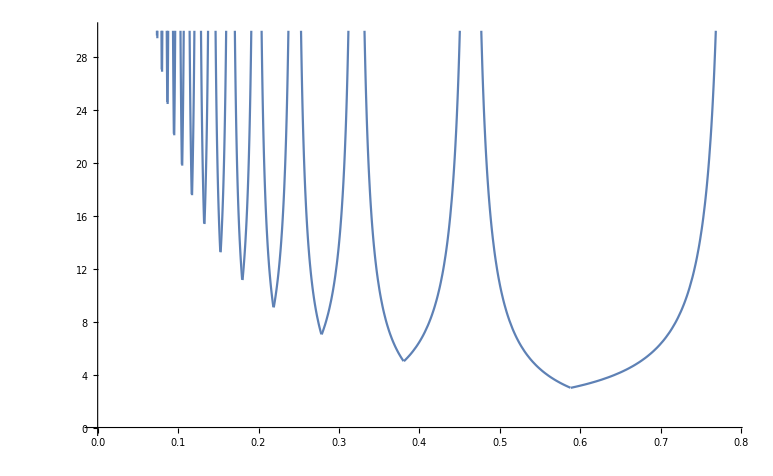

```mathematica
Show[Plot[Distance[x], {x, 0.05, Pi/4}, PlotRange->{{0,Pi/4},{0, 30}}]]
```

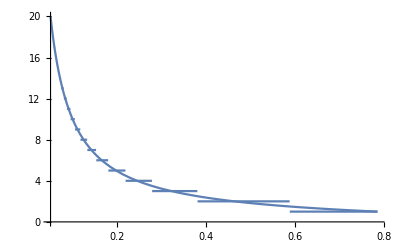

```mathematica
Show[Plot[Round[Cot[x]], {x, 0.05, Pi/4}, PlotRange->{{0.05, Pi/4},{0, 20}}], Plot[Cot[x], {x, 0.05, Pi/4}, PlotRange->{{0.05, Pi/4},{0, 20}}]]
```